# Determining Complexities of Chaotic Systems Through Analysis of Their Fractal Dimensions

Charlie Bushman
Start: 05/09/18
Phys 234

## Section 01 : Introduction

In this notebook, we will be looking at dissipative chaotic systems and how to make use of their periodicity, and the fractals arising from this property, to determine their complexities. Many of these terms, even if they are things you have heard in other contexts, need to be carefully defined for this project so we’ll begin with some definitions.

1. Dissipative Chaotic Systems:
	A system is a chunk of the universe that we decide to look at in great detail. A pool table, for example, is a system wherein there are some point-like masses and a rectangular boundary. This is a good system to consider because it is largely isolated from its environment (meaning stuff around it, like air or a lamp, doesn’t have much effect on what happens) and it exhibits some chaotic behaviors. A chaotic system can be (over)simply defined as one in which very small changes in initial conditions can result in vastly different dynamics within the system. Take the pool table; when you’re starting a game and you have to break the triangle, it never breaks the same way twice. This is because tiny changes in the angle and speed at which you hit the cue ball cause completely different things to happen in the system. A pool table is also a dissipative system because there is a force taking energy out of the system: friction. This just means that the particles in the system will continue to slow down over time. We will see why this is important in the next definition.
2. Periodicity: 
	An odd but very cool feature of chaotic systems is that they are periodic. This means that if a chaotic system with one “object” in it starts at point A it will eventually return there with the same velocity it had when it started. However, this feature has to be amended for dissipative chaotic systems because the path traced out by the “object” in a dissipative chaotic system is going to get smaller and smaller with each period meaning that instead of returning to point A it will return to point A’ which will just be a lower energy state version of A. This means that it will be tracing out the same pattern but smaller and smaller each time. And this leads us into fractals...
3. Fractals (Fractal Dimensions):
	A fractal is a curve or geometric figure that is self-similar at any scale. This means that it should look the same whether you’re looking at the whole thing or just a tiny piece of it. A relatively simple example of this is shown in Figures 1.1 and 1.2. Fractals can be found in lots of interesting places in nature and one of those is dissipative chaotic systems. To quote the last definition: “ it will be tracing out the same pattern but smaller and smaller each time.”
	-Graphics-                            -Graphics-
	Figure 1.1: The Sierpinski Carpet                                   Figure 1.2: The top left corner of Figure 1.1 
	The fractal dimension of a chaotic system is not actually one well defined quantity because there are a number of different “dimensions” that a chaotic system has and that can be measured. In this notebook we will be looking at the fractal dimension as if the path of the system is simply a fractal pattern. This means that we will be measuring it using both the box counting method and the correlation function in Section 2.0.
4. Complexity:
	Complexity is a term that can take a huge variety of meanings throughout physics and even in the context of fractals. In this project, we will be defining complexity as the amount of space that a chaotic system’s path fills. Basically this means that, if we consider the path of a fractal to be a one dimensional curve, then the amount of 2D space that it fills is the complexity of the system.

With these definitions in mind, this notebook will be broken up into seven sections (including this intro). The second will contain statistical functions for calculating the fractal dimension such as the box counting function and the correlation function. The third and fourth sections will be focused on analyses of the Henon map and the Tinkerbell map (aka as Henon/Tinkerbell attractor), both of which are chaotic systems. The fifth and sixth sections will be focused on the same maps but this time on how their fractal dimensions change over changes in their parameters. The final section will be a conclusion.

## Section 02 : Needed Packages And Statistical Functions

This section is home to two methods that calculate the fractal dimension (FD) of an input map of a system. The first method is a box counting method that takes in a Graphics object for its only argument. It then overlays boxes of varying sizes over the image and counts the number of points in each box and sums these, each divided by the total number of points. In this way, with different size boxes being overlaid on each iteration, it can find the space filling capability of the fractal at many scales.
The second method does something very similar but takes a slightly more mathematical approach to it. The input is a list of points now. Instead of overlaying boxes, it looks at each point individually and counts up all the points within an input radius. It then does the same dividing and summing as the box counting method. Over a range of radius inputs, this should provide an exponential curve with an exponent that is the fractal dimension.
The third method is a function that determines the radius of gyration of the input cluster. This is important to determine because the correlation function starts giving variable results once the input radius reaches and surpasses the radius of gyration.
The main reason to have two different methods for making the same calculation is that it will provide an easy check on the accuracy of both of them; if they come out the same it is probably working, otherwise it probably isn’t.

### Scaling Squares Measurement Technique: Measures the fractal dimension of the input image

```mathematica
squaresMethod[imgInput_]:=Module[{img=imgInput,bin,seq,result},
img=ImageResize[img,{720,360}];
bin=LocalAdaptiveBinarize[ImageAdjust[img,0.3],200,{0.9,0,0}];
seq=Reverse[Intersection@@Divisors/@ImageDimensions[img]];

{width,height}=ImageDimensions[img];
result={width/#,Last@First@ImageLevels@Image[BlockMap[Min,ImageData[bin],{#,#}],"Bit"]}&/@seq;

fm=LinearModelFit[Log[result],{1,x},x];
{ListLogLogPlot[result],Plot[fm[x],{x,0,720}],Return[fm["ParameterTable"]],Normal[fm][[2]]/x}
]
```

### Correlation Function Technique: Measures the fractal dimension of the input points which should be the product of a mapping function

```mathematica
correlationFunction[listOfData_,radius_]:=Module[{data=listOfData,r=radius},
(*ballOfR=1/(Length[data]-1)*Sum[If[i<j,HeavisideTheta[r-EuclideanDistance[data[[i]],data[[j]]]],0],{i,Length[data]},{j,Length[data]}];*)

1/(Length[data]*(Length[data]-1))*Sum[If[i≠j,If[r-EuclideanDistance[data[[i]],data[[j]]]>0,1,0],0],{i,Length[data]},{j,Length[data]}]//N
]
```

#### Radius of Gyration : Used to Calculate the Ideal Range for Determining the Fractal Dimension

```mathematica
radiusOfGyr[clus_]:=Module[
{sites=clus,numSites=Length[clus],xVals,yVals,xAve,yAve},

xVals=Table[Take[sites[[i]],1],{i,numSites}];
yVals=Table[Take[sites[[i]],-1],{i,numSites}];

xAve=Mean[xVals];
yAve=Mean[yVals];

Mean[Table[(xVals[[i]]-xAve)^2+(yVals[[i]]-yAve)^2,{i,numSites}]][[1]]
]
```

## Section 03 : Analysis of the Henon Dissipative Map for One Parameter Set

In this section, we will be looking at the Henon dissipative map for a single parameter set. The parameters we will be using are α = 1.4 and β = 0.3. There are three subsections, the first of which will focus on generating the Henon map and the second and third of which will focus on calculating the fractal dimension of the resultant map from the first subsection.
We will be looking at the Henon map because it is a very well known chaotic attractor which is a relatively light computational load to simulate. The benefit of it being well known is that there are many studies on the Henon attractor and thus many sources to verify results we find here.

### Section 03.1 : Generating the Henon Map

Here we will be developing and testing our function for generating Henon maps. The basic idea behind a mapping function is that it is a function that takes in a coordinate and then applies some transformation to it that translates physically to the movement of a particle over a specific time step. The function is used over and over again to create a list of points that trace out the path of the particle over time. This method is preferable to actually tracing the path of the particle because a path cannot be input into the correlation function.
The Henon map works on the equations:
	x_(n+1) = 1 - α(x_n)^2 + y_n
	y_(n+1) = βx_n
Meaning that it takes in a coordinate pair (x_n, y_n) and then outputs (x_(n+1), y_(n+1)) according to these equations. The NestWhileList[] function will repeat this process until one of a number of checks returns false. The coordinate pairs it returns are turned into a graphics object that is then output from the function. We will then run a test with values of α = 1.4 and β = 0.3 for which we have a reference value for the FD.

```mathematica
henonPlotFunction[a_,b_]:=Module[{dataPoints},
dataPoints=Drop[NestWhileList[{1-a#[[1]]^2+#[[2]],b#[[1]]}&,{0,0},#.#<100.&,1,5^4],10];
{dataPoints,Graphics[{Red,
PointSize[.0005],
Point/@dataPoints
}]}
]
```

```mathematica
henonPlot=henonPlotFunction[1.4,0.3];
```

```mathematica
(*This line is worth keeping in the notebook because it shows why we need to resize the images in the squaresMethod to 360 by 720. The number of divisors of the sidelengths is the number of sizes of squares that can be evenly overlaid onto the image for counting.*)
Intersection[Divisors[360],Divisors[720]]
```

{1,2,3,4,5,6,8,9,10,12,15,18,20,24,30,36,40,45,60,72,90,120,180,360}

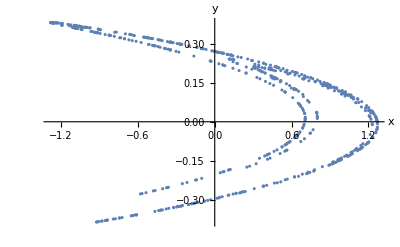

```mathematica
ListPlot[henonPlot[[1]],AxesLabel->{x,y}]
```

Figure 3.1 : Henon Map for α = 1.4 and β = 0.3
	The self-similar properties of this attractor that make the map a fractal are fairly easy to see. The smaller bends within the largest horseshoe make their own horseshoes, sometimes with different orientations.

### Section 03.2 : Analyzing the Fractal Dimension of the Henon Map by Means of squaresMethod[]

This subsection will be focused on finding the fractal dimension of the Henon map produced above (Figure 3.1) using the squaresMethod[]. We will also see an animation of the process that the squaresMethod[] uses to make its calculations.
A brief note on the squaresMethod[] output: The output is a list of four elements. The first (henonData[[1]] in this case) is the log-log list of data it calculated, the second is the best fit line for that data calculated with LinearModelFit[]. The third is the ParametersTable for the best fit line including the estimated fractal dimension and the error bound. The fourth is the FD estimate returned as a number, separate of the table.

```mathematica
henonData=squaresMethod[henonPlot[[2]]];
```

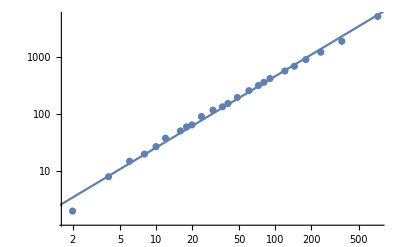

```mathematica
Show[henonData[[1]],henonData[[2]]]
```

Figure 3.2 : Log - Log Plot of the squaresMethod[] for the Henon Map
	The log of the data fits a linear model very well and it can be seen in the table below that the slope of this linear model is very near to the researched value for the fractal dimension of the system.

```mathematica
henonData[[3]]
henonData[[4]]
```

Return[ | Estimate | Standard Error | t-Statistic | P-Value
1 | 0.371028 | 0.082026 | 4.5233 | 0.000168034
x | 1.25361 | 0.0209877 | 59.7307 | 7.72604×10^-26]

1.25361

```mathematica
sz=252;
bin=LocalAdaptiveBinarize[ImageAdjust[henonPlot[[2]],0.3],200,{0.9,0,0}];
seq=Reverse[Intersection@@Divisors/@{360,720}];
imgs=Image[BlockMap[Min,ImageData[bin],{#,#}],"Bit"]&/@seq;
```

```mathematica
imgs=If[First@ImageDimensions[#]>sz,ImageResize[Image[#,Real],sz],(*downscale as grayscale*)ImageResize[#,sz,Resampling->"Nearest"]]&/@imgs;(*upscale as bitmap*)frm=Table[ImageCompose[ImageResize[henonPlot[[2]],252],{im,0.5}],{im,imgs}];

ListAnimate[frm]
```

Figure 3.3 : Animation of the squaresMethod[] Being Run on the Henon Map
	This animation shows the successively smaller squares that are overlaid on the map to produce the results in Figure 3.2.

### Section 03.3 : Analyzing the Fractal Dimension by Means of the correlationFunction[]

In this subsection, we will be using the correlationFunction[] from Section 02 to determine the fractal dimension of the Henon map we made earlier in this section. We will do this by making a table of correlation values from radii of just over zero up to the radius of gyration of the map. By then plotting the log of that data and getting a linear fit model we should be able to calculate the fractal dimension of the system which (hopefully) will match that from subsection 03.2.

```mathematica
radiusOfGyr[henonPlot[[1]]]
```

0.573744

```mathematica
correlations=Table[{i,correlationFunction[henonPlot[[1]],i]},{i,0.1,radiusOfGyr[henonPlot[[1]]],0.10}]
```

{{0.1,0.0430578},{0.2,0.0988227},{0.3,0.16598},{0.4,0.239098},{0.5,0.307328}}

FittedModel[-0.318675+1.23009 x]

| Estimate | Standard Error | t-Statistic | P-Value
1 | -0.318675 | 0.0162444 | -19.6176 | 0.000289393
x | 1.23009 | 0.0111243 | 110.576 | 1.63063×10^-6

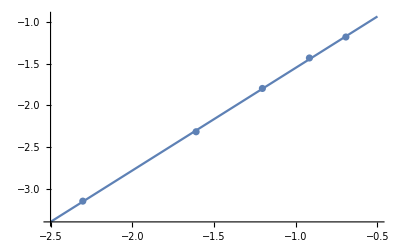

```mathematica
(*Clears x to avoid problems with it being treated as a variable with a preset value by LinearModelFit[]*)
Clear[x]
expFit=LinearModelFit[Log[correlations],{1,x},x]
expFit["ParameterTable"]
Show[Plot[expFit[x],{x,-2.5,-0.5}],ListPlot[Log[correlations]]]
```

Figure 3.4 : Results of the correlationFunction[] Run on the Henon Map
	This plot shows the log of the data from the correlationFunction[]. Once again it provides a very linear trend with a slope that matches the fractal dimension we expect.

According to Eric W. Weisstein’s Henon Map article on wolfram mathworld and Estimating fractal dimension by James Theiler, the fractal dimension of the Henon map with parameters α = 1.4 and β = 0.3 should be 1.25 ± 0.02. This matches very well with our results in this section. With the squaresMethod[] we got 1.25 ± 0.02 and with the correlationFunction[] we got 1.23 ± 0.01, both of which fall within the error bars for the researched value. Thus, we can conclude that our two methods for calculating the fractal dimension of a chaotic system is working (at least for this system with these parameters). In the next section we will test our methods further on the Tinkerbell attractor.

## Section 04 : Analysis of the Tinkerbell Map for One Parameter Set

This section will be very similar to the last section with really the only difference being that we are working with the Tinkerbell attractor instead of the Henon attractor. We will again be using only one unchanging set of parameters in this section and we will be using both methods to try to get a fractal dimension that matches up with our researched value of 1.3992 from Bifurcation and chaos in the Tinkerbell map.

### Section 04.1 : Generating the Tinkerbell Map

To generate the Tinkerbell map, we are using a very similar to mapping function to the Henon map but this time with equations for the Tinkerbell map instead. The equations it is based on are:
	x_(n+1) = (x_n)^2 - (y_n)^2 + ax_n + by_n
	y_(n+1) = 2 x_n y_n + cx_n + dy_n
The values we will be using for a, b, c, and d in this section are a = 0.9, b = -0.5, c = 2.3594, and d = 0.5.

```mathematica
tinkerbellMapFunction[a_,b_,c_,d_]:=Module[{pointsList},
pointsList=Drop[NestWhileList[{(#[[1]])^2-(#[[2]])^2+a*#[[1]]+b*#[[2]],2*#[[1]]*#[[2]]+c*#[[1]]+d*#[[2]]}&,{-0.72,-0.64},#.#<100.&,1,25000],1];

{pointsList,Graphics[{Red,
PointSize[.0005],
Point/@pointsList
}]}
]
```

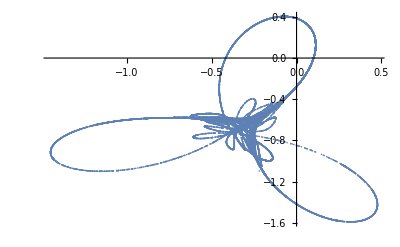

```mathematica
tinkerbellMap01=tinkerbellMapFunction[0.9,-0.5,2.3594,0.5];
tinkerbellMap01[[2]];
ListPlot[tinkerbellMap01[[1]]]
```

Figure 4.1 : A Plot of the Tinkerbell Map for Parameters a = 0.9, b = -0.5, c = 2.3594, and d = 0.5
	This plot shows the Tinkerbell map which we will be working with in this section.

### Section 04.2 : Analyzing the Tinkerbell Map by Means of the squaresMethod[]

In this subsection, we will be calculating the fractal dimension of the Tinkerbell map using the squaresMethod[]. Same process as with the Henon map.

```mathematica
tinkerbellData01=squaresMethod[tinkerbellMap01[[2]]];
```

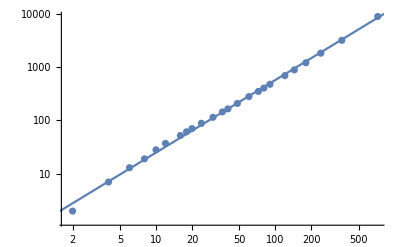

```mathematica
Show[tinkerbellData01[[1]],tinkerbellData01[[2]]]
```

Figure 4.2 : Results of the squaresMethod[] Run on the Tinkerbell Map
	These results are again very linear and provide a result that is close to the result we want of 1.39.

```mathematica
tinkerbellData01[[3]]
```

Return[ | Estimate | Standard Error | t-Statistic | P-Value
1 | 0.0863658 | 0.0539912 | 1.59963 | 0.123945
x | 1.35921 | 0.0138145 | 98.39 | 1.37128×10^-30]

### Section 04.3 : Analyzing the Tinkerbell Map by Means of the correlationFunction[]

In this subsection, we will be calculating the fractal dimension of the Tinkerbell map using the correlationFunction[]. Same process as with the Henon map.

```mathematica
shorterTinkerList=Table[tinkerbellMap01[[1,i]],{i,1,Length[tinkerbellMap01[[1]]],200}];
Length[shorterTinkerList]

tinkerRadius=radiusOfGyr[shorterTinkerList]

correlations=Monitor[Table[{k,correlationFunction[shorterTinkerList,k]},{k,0.05,tinkerRadius,0.025}],k]
```

500

0.218436

{{0.05,0.0291222},{0.075,0.0500922},{0.1,0.0776914},{0.125,0.105916},{0.15,0.133315},{0.175,0.163968},{0.2,0.195118}}

FittedModel[0.603956+1.38099 x]

| Estimate | Standard Error | t-Statistic | P-Value
1 | 0.603956 | 0.0334743 | 18.0424 | 9.60834×10^-6
x | 1.38099 | 0.0150701 | 91.6372 | 2.93353×10^-9

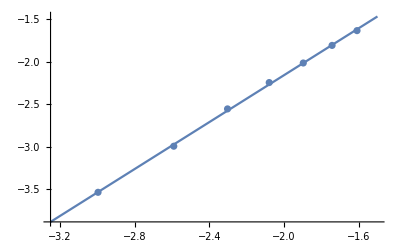

```mathematica
Clear[x]
expFit=LinearModelFit[Log[correlations],{1,x},x]
expFit["ParameterTable"]
Show[Plot[expFit[x],{x,-3.25,-1.5}],ListPlot[Log[correlations]]]
```

Figure 4.3 : Results of the correlationFunction[] Run on the Tinkerbell Map
	Again, we receive a very linear log plot with a slope of 1.38 which is very close to the researched value for the fractal dimension of the Tinkerbell Map and is within the error bar.

This section has gotten results almost as good as Section 03 with the Henon map. Here we got one value for the fractal dimension that is within the error bound from the correlationFunction[], 1.38 ± 0.02 and one value that is just outside the error bound from the squaresMethod[], 1.36 ± 0.01. The researched value we are using as the true value comes from Bifurcation and chaos in the Tinkerbell map and is 1.3992. The lower value for the squaresMethod[] is not entirely unreasonable either, because the center of the map is so densely packed that it may skew calculations for smaller square overlays. This is an unfortunate defect, but one we’ll have to live with because it cannot be easily remedied.

## Section 05 : Consolidating Methods into One Function

This section is being used to consolidate all of the work done in Sections 03 and 04 into one function. The idea behind it is that one should be able to input a list of points from a mapping function, those points as a Graphics object, and a caption to describe what the map is that is being input and then get out all the information from the last two sections. Unfortunately, the use of both methods is doubly time consuming so in future sections where we are looking at change in FDs over parameters, we will just be using the squaresMethod[] and not this.

```mathematica
fractalDim[points_,img_,caption_]:=Module[
{map=img,dataPoints=points,squareData,corrData,shorterList,gyrRad,step,expFit},

squareData=squaresMethod[map];

shorterList=If[Length[dataPoints]>501,Table[dataPoints[[n]],{n,1,Length[dataPoints],Floor[Length[dataPoints]/500]}],dataPoints];
gyrRad=radiusOfGyr[dataPoints];
step=(gyrRad-0.05)/5;
corrData=Monitor[Table[correlationFunction[shorterList,rad],{rad,0.05,gyrRad,step}],rad];

Clear[x];
expFit=LinearModelFit[Log[corrData],{1,x},x];
expFit={ListPlot[Log[correlations]],Plot[expFit[x],{x,-3.25,-1.5}],expFit["ParameterTable"],Normal[expFit][[2]]/x};

(*Stuff we want to show at the end of this function:
1. The map itself
2. Simple log-log list plots for both methods
3. Parameter tables for both methods
4. Averaged value for fractal dimension
*)
{caption,map,squareData[[1]],squareData[[2]],expFit[[1]],expFit[[2]],squareData[[3]],expFit[[3]],squareData[[4]],expFit[[4]]}
]
```

### Code Check

```mathematica
henonPlot02=henonPlotFunction[1.4,0.3];
```

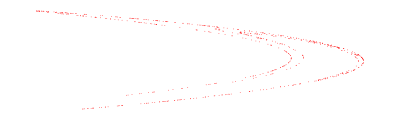
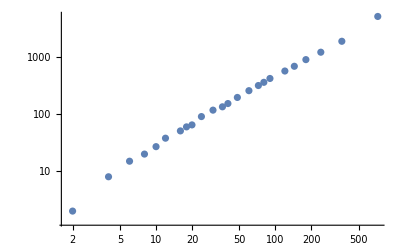
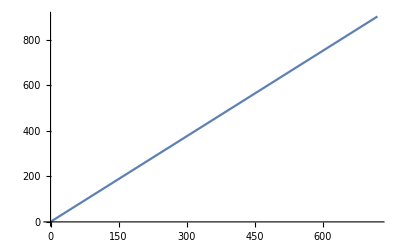
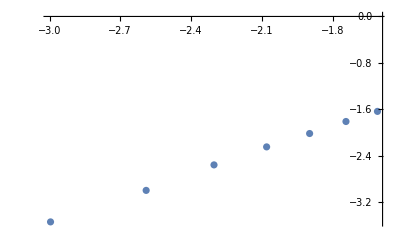
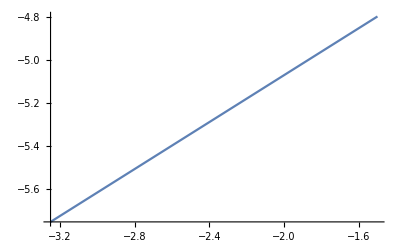
{Tinkerbell Map for a = 0.9, b = -0.5, c = 2.3594, d = 0.5,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,Return[ | Estimate | Standard Error | t-Statistic | P-Value
1 | 0.371028 | 0.082026 | 4.5233 | 0.000168034
x | 1.25361 | 0.0209877 | 59.7307 | 7.72604×10^-26], | Estimate | Standard Error | t-Statistic | P-Value
1 | -3.97518 | 0.35844 | -11.0902 | 0.00037602
x | 0.547161 | 0.092039 | 5.94488 | 0.00401602,1.25361,0.547161}

```mathematica
fractalDim[henonPlot02[[1]],henonPlot02[[2]],"Tinkerbell Map for a = 0.9, b = -0.5, c = 2.3594, d = 0.5"]
```

There is also an error with the correlationFunction[] in this consolidated function. For some reason it will only return very small values for the fractal dimension that are not right at all, despite the same function working fine independently. Since this function is not used anywhere in the project, I’ve just closed this section and leave it as a challenge for the future to fix and make use of it.

## Section 06 : Analysis of the Henon Plot Over a Range of Parameters

Now we are getting into the interesting part of this project where we will be looking for patterns in the change of the fractal dimension with changes in the system parameters. In this first section of parameter changes, we will be looking at the Henon map, first at variations in the β parameter and then at changes in both the α and β parameters. The goal of this section and the next is to find a trend or pattern in the change of the fractal dimension over changes in parameters because such a trend or pattern would lend some sort of predictability to these chaotic systems.

### Section 06.1 : Variation in the Beta Parameter

In this first subsection, we will be looking at how the Henon map’s complexity changes over changes in the β parameter. To do this effectively, it is necessary to look at changes on multiple scales, meaning on varying step sizes for the β parameter. For example, in this section we are looking at a data set that ranges from 0.99 to 0.999 by steps of 0.001, then from 0.999 to 1.000 by steps of 0.0001, and then from 1.001 to 1.010 again by steps of 0.001. This varied resolution over the data set is necessary because it will hopefully discredit any apparent trends on larger or smaller scales that aren’t actually there.

```mathematica
henonDataPoint2=Table[henonPlotFunction[0.2,i],{i,0.999,1.0,0.0001}];
extraHenonDataPoint2=Table[henonPlotFunction[0.2,i],{i,0.99,0.999,0.001}];
moreHenonDataPoint2=Table[henonPlotFunction[0.2,i],{i,1.001,1.010,0.001}];
imgsPoint2=Table[extraHenonDataPoint2[[i,2]],{i,1,Length[extraHenonDataPoint2]}];
AppendTo[imgsPoint2,Table[henonDataPoint2[[i,2]],{i,1,Length[henonDataPoint2]}]];
AppendTo[imgsPoint2,Table[henonDataPoint2[[i,2]],{i,1,Length[moreHenonDataPoint2]}]];
imgsPoint2=Flatten[imgsPoint2];
ListAnimate[imgsPoint2]
```

Figure 6.1 : Animation of the Evolution of the Henon Map Over the β Parameter
	This animation shows the Henon map evolving over the range 0.99 to 0.999 by steps of 0.001, then from 0.999 to 1.000 by steps of 0.0001, and then from 1.001 to 1.010 again by steps of 0.001.

```mathematica
bValues=Flatten[AppendTo[Table[i,{i,0.99,0.999,0.001}],AppendTo[Table[i,{i,0.999,1.0,0.0001}],Table[i,{i,1.001,1.010,0.001}]]]];
henonFractalDimsPoint2=Table[{bValues[[i]],squaresMethod[imgsPoint2[[i]]][[4]]},{i,1,30}]
```

Set::write: Tag Table in Table[i,{i,0.999,1.,0.0001}] is Protected.

Set::write: Tag Table in Table[i,{i,0.99,0.999,0.001}] is Protected.

{{0.99,1.14977},{0.991,1.16565},{0.992,1.17803},{0.993,1.1889},{0.994,1.19113},{0.995,1.18446},{0.996,1.02544},{0.997,1.20295},{0.998,1.21435},{0.999,1.18434},{0.999,1.18434},{0.9991,1.12455},{0.9992,1.19118},{0.9993,1.18432},{0.9994,1.1917},{0.9995,1.17371},{0.9996,1.15393},{0.9997,1.17671},{0.9998,1.14501},{0.9999,1.02233},{1.,1.03987},{1.001,1.18434},{1.002,1.12455},{1.003,1.19118},{1.004,1.18432},{1.005,1.1917},{1.006,1.17371},{1.007,1.15393},{1.008,1.17671},{1.009,1.14501}}

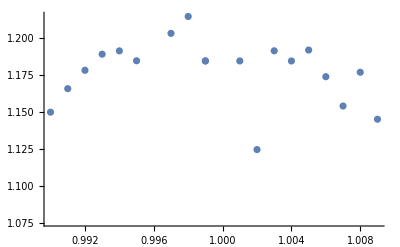

```mathematica
ListPlot[Table[{henonFractalDimsPoint2[[i,1]],henonFractalDimsPoint2[[i,2]]},{i,Join[Range[1,11],Range[21,30]]}]]
```

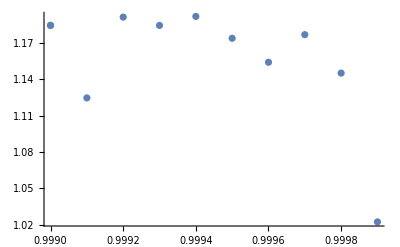

```mathematica
ListPlot[Table[{henonFractalDimsPoint2[[i,1]],henonFractalDimsPoint2[[i,2]]},{i,Range[10,20]}]]
```

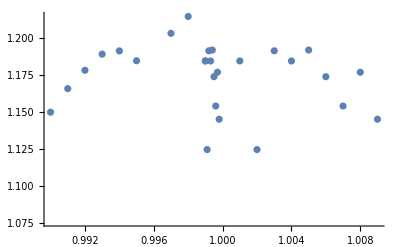

```mathematica
ListPlot[Table[{henonFractalDimsPoint2[[i,1]],henonFractalDimsPoint2[[i,2]]},{i,1,30}]]
```

Figure 6.2 : Plots of the Fractal Dimension of the Henon Map Over Changes in the β Parameter
	You can see that in the first two plots there isn’t obviously any pattern but there also isn’t any obvious lack of a pattern. However, with the combination of the two data sets in the third plot, it becomes fairly apparent that there is no pattern to be seen here.

### Section 06.2 : Variation in Both the Alpha and the Beta Parameters

In this subsection, we are looking at changes over both the α and β parameters. This time we will be considering ranges of α from 0.0 to 0.3 and β from 0.9 to 1.1, both by steps of 0.05. Hopefully by looking at plots of the change in the complexity of the system over two variables it will be easier to see some sort of trend.

```mathematica
aRange=Range[0.0,0.3,0.05];
bRange=Range[0.9,1.1,0.05];
henonDataVaried=Table[henonPlotFunction[i,j],{i,aRange},{j,bRange}];
imgsVaried=Table[henonDataVaried[[i,j,2]],{i,1,Length[aRange]},{j,1,Length[bRange]}];
ListAnimate[Flatten[imgsVaried]]
```

Figure 6.3 : Animation of the Evolution of the Henon Map Over Changes in the α and β Parameters
	This animation shows the evolution of the Henon map over a range of β values for one α value and then for successive α values (a kind of snake like pattern if you picture them on a grid). You can see how there is little visible evidence suggesting patterning.

```mathematica
henonFractalDimsVaried=Flatten[Table[{(i/20)//N,((j/20)+0.9)//N,squaresMethod[imgsVaried[[i,j]]][[4]]},{i,1,Length[aRange]},{j,1,Length[bRange]}],1]
```

{{0.05,0.95,0.480286},{0.05,1.,0.31816},{0.05,1.05,0.209003},{0.05,1.1,0.365451},{0.05,1.15,0.535555},{0.1,0.95,0.832656},{0.1,1.,0.8945},{0.1,1.05,0.472797},{0.1,1.1,0.389228},{0.1,1.15,0.400879},{0.15,0.95,0.785825},{0.15,1.,0.880187},{0.15,1.05,1.0981},{0.15,1.1,0.353113},{0.15,1.15,0.302025},{0.2,0.95,0.817803},{0.2,1.,0.905474},{0.2,1.05,1.13158},{0.2,1.1,0.383806},{0.2,1.15,0.310673},{0.25,0.95,0.818386},{0.25,1.,0.934548},{0.25,1.05,1.03987},{0.25,1.1,0.307021},{0.25,1.15,0.239986},{0.3,0.95,0.782834},{0.3,1.,0.878314},{0.3,1.05,0.415175},{0.3,1.1,0.362352},{0.3,1.15,0.381431},{0.35,0.95,0.810492},{0.35,1.,0.914574},{0.35,1.05,0.993813},{0.35,1.1,0.274892},{0.35,1.15,0.275722}}

```mathematica
ListPlot3D[henonFractalDimsVaried,AxesLabel->{α,β,FD}]
```

-Graphics3D-

Figure 6.4 : Plot of the Fractal Dimension of the Henon Map Over Changes in the α and β Parameters
	This plot shows the FD varying as a function of α and β. You can see that there appears to be a bit of a trend along the β axis for the FD to either rise or fall at the same β value but it is not a very strong trend.

Because of the interesting trends visible in the plot above, we will now be looking at a smaller range with higher resolution to see if the pattern holds on a smaller scale. Specifically, we will be looking at β for a range of 0.95 to 1.00 with a five times higher resolution of 0.01.

```mathematica
aRange2=Range[0.23,0.28,0.01];
bRange2=Range[0.95,1.00,0.01];
henonDataVaried2=Table[henonPlotFunction[i,j],{i,aRange2},{j,bRange2}];
imgsVaried2=Table[henonDataVaried2[[i,j,2]],{i,1,Length[aRange2]},{j,1,Length[bRange2]}];
ListAnimate[Flatten[imgsVaried2]]
```

Figure 6.5 : Animation of the Evolution of the Henon Map Over Smaller Changes in the α and β Parameters
	This animation shows the same progression as Figure 6.3 but with a higher resolution meaning that the change in parameters with each stage of the animation is five times smaller.

```mathematica
henonFractalDimsVaried2=Flatten[Table[{((i/100)+0.23)//N,((j/100)+0.95)//N,squaresMethod[imgsVaried2[[i,j]]][[4]]},{i,1,Length[aRange2]},{j,1,Length[bRange2]}],1]
```

{{0.24,0.96,0.899461},{0.24,0.97,0.947782},{0.24,0.98,0.957397},{0.24,0.99,1.03754},{0.24,1.,1.18861},{0.24,1.01,0.678455},{0.25,0.96,0.882217},{0.25,0.97,0.896914},{0.25,0.98,0.950371},{0.25,0.99,1.01592},{0.25,1.,0.679411},{0.25,1.01,0.415419},{0.26,0.96,0.878314},{0.26,0.97,0.892773},{0.26,0.98,0.941293},{0.26,0.99,1.03325},{0.26,1.,1.09375},{0.26,1.01,0.415175},{0.27,0.96,0.888093},{0.27,0.97,0.907705},{0.27,0.98,0.959039},{0.27,0.99,1.01007},{0.27,1.,1.16277},{0.27,1.01,0.584986},{0.28,0.96,0.894056},{0.28,0.97,0.929804},{0.28,0.98,0.970776},{0.28,0.99,1.03503},{0.28,1.,1.05997},{0.28,1.01,0.703175},{0.29,0.96,0.920109},{0.29,0.97,0.96956},{0.29,0.98,0.979055},{0.29,0.99,1.04811},{0.29,1.,1.2015},{0.29,1.01,0.762912}}

```mathematica
ListPlot3D[henonFractalDimsVaried2,AxesLabel->{α,β,FD}]
```

-Graphics3D-

Figure 6.6 : Plot of the Fractal Dimension of the Henon Map Over Smaller Changes in the α and β Parameters
	This plot shows the plot of the fractal dimension as a function of α and β for a smaller range of  α and β values and for higher resolutions of both. The same ridge that was apparent in Figure 6.4 is also apparent here as is the declining plateau out to one side of it.

Despite the higher resolution, the second plot appears to just be a zoomed in image of the first, which is promising evidence supporting a conclusion that the fractal dimension might follow a trend decided by the β parameter. It is also entirely possible that I just picked a few lucky points and it just happens to look the same because of that.

## Section 07: Analysis of the Tinkerbell Map Over a Range of Parameters

In this section, we will doing the same thing as in Section 06 but this time with the Tinkerbell map. Because the Tinkerbell map has four parameters and there is no easy way to graph changes over four parameters, we are going to look at change in one parameter, c, and if there is nothing promising there, redirect attention to the more promising Henon map.

### Section 07.1 : Variation in the C Parameter

Here we are looking at how changes in the c parameter will affect the fractal dimension. Following the same process as with the Henon map, we can see that there is very little evidence of any trends or patterns in the results.

```mathematica
cRange=Range[2.00,2.40,0.05];
tinkerDataC=Table[tinkerbellMapFunction[0.9,-0.5,i,0.5],{i,cRange}];
tinkerImgs=Table[tinkerDataC[[i,2]],{i,Length[tinkerDataC]}];
ListAnimate[tinkerImgs]
```

Figure 7.1 : Animation of the Evolution of the Tinkerbell Map Over Changes in the C Parameter
	This animation shows the evolution of the Tinkerbell map for a range of c values from 2.00 to 2.40 by steps of 0.05. Like the Henon map, the changes exhibited by this system can appear very chaotic.

```mathematica
tinkerFractalDimsC=Table[{(2+i/20)//N,squaresMethod[tinkerImgs[[i]]][[4]]},{i,Length[tinkerImgs]}]
```

{{2.05,1.05177},{2.1,0.825821},{2.15,1.26213},{2.2,1.27736},{2.25,1.30347},{2.3,1.01234},{2.35,1.22978},{2.4,1.34703},{2.45,0.638883}}

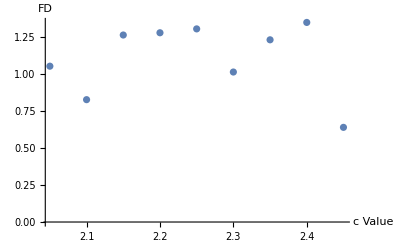

```mathematica
ListPlot[tinkerFractalDimsC,AxesLabel->{"c Value","FD"}]
```

Figure 7.2 : Plot of the Fractal Dimension of the Tinkerbell Map Over Changes in the C Parameter
	There is no evidence of patterning here. It could be hidden as with the β plot for the Henon map but it would not be easy to uncover if it is hidden because there are three other parameters to deal with here rather than just the one other that the Henon plot has.

Like with the changes in the β parameter for the Henon map, there is no obvious sign of patterning to this data. It could be that with further investigation of the other three parameters we might find interesting trends like with the Henon map but without some way to narrow down what exactly to look for, that could be a project all to itself.

## Section 08 : Conclusion

The only reason anyone would be interested in this work for practical reasons is if I can actually find a pattern that would give some sort of predictive power over the complexity of a system. And in order to have predictive power, we need to have a function or a trend that can describe the exact relation between the FD and one or more of the parameters. Whether or not I have actually succeeded in finding such a pattern is not entirely clear and would require more simulations to verify but it does appear, just on the bases of the two plots from Section 06, that there might be a pattern.The first graph is a plot of the fractal dimension versus the two parameters for the Henon function. The second graph runs over a smaller range of β values with higher resolution. In other tests of this sort, where I enhance the resolution to look at a smaller section, I usually get results that are just as erratic as the original results but within that smaller window.This case is different though, because here, the enhanced resolution looks almost identical to the original.This may mean that there is a trend linking the FD and β values which could be found for any α. It' s also possible that I just picked some particularly nice looking points and got a deceptively nice looking graph as a result. There is certainly evidence elsewhere in the project to refute the patterning found here.
	The major takeaway from this project is uncertain at best which is not ideal, but it does warrant further investigation into the subject. Perhaps more importantly, this project sets solid groundwork for this continuing investigation. I now have a very easy-to-use method with verified results to determine the fractal dimension and thus the complexity of chaotic systems. Possibilities for further research include looking more for patterns between parameters and the fractal dimension of a system, looking for ways to better deal with problems in the methods for calculating fractal dimensions, and looking into what the various types of fractal dimensions of a system are (yes, there are many of them!) and if there are any patterns to be found in these FDs with parameters.

## Appendices

### Appendix A : Sources

Bifurcation and chaos in the Tinkerbell map: Shaoliang Yuan, Zhujun Jing, & Tao Jiang
	This article is largely stuff that I did not use for this project. The part that I did use is on pages 3150 and 3151 where there is a series of images with descriptions for each. This is where I got my values for the fractal dimension of a Tinkerbell map for Section 04 and how I decided on a range of c values to use for Section 07.
	
chaos-math.org/en: Jos Leys, Étienne Ghys and Aurélien Alvarez
	This website was very helpful in getting me started with this project. They have an hour and a half long video broken up into nine chapters all on introducing people to chaos and chaotic systems. A lot of the foundational knowledge of this project comes from this website.
	
Estimating fractal dimension: James Theiler
	I learned how to implement the correlation function for a fractal created by a mapping function from this article and I found one of the maps I would be using (Henon) along with a value for its fractal dimension at the parameter values I used in Section 03.
	
Henon Map: Eric W. Weisstein from MathWorld
	This site provides a bit of information on the Henon map including what equations are used in its mapping function and what the expected value for the fractal dimension should be for the parameters used in Section 03 (matching the value given in Theiler’s article).
	
Measuring the fractal dimension of a tree photo: Szabolcs Horvat
	This is the article in which the squaresMethod[] is developed and where the code is pulled from. The code was originally developed to determine the fractal dimension of a photo of tree branches but works very well on maps of chaotic systems as well.

### Appendix B : Code Development and Checks

#### squaresMethod[]

Development : Section 02
Check : Sections 03.2 and 04.2

#### correlationFunction[]

Development : Section 02
Check : Sections 03.3 and 04.3

#### Henon Map

Development : Section 03.1
Check : Sections 03.1 and 06

#### Tinkerbell Map

Development : Section 04.1
Check : Sections 04.1 and 07

### Appendix C : Figures and Plots

Figure 1.1 : The Sierpinski Carpet
Figure 1.2 : The top left corner of Figure 1.1 
Figure 3.1 : Henon Map for α = 1.4 and β = 0.3
Figure 3.2 : Log - Log Plot of the squaresMethod[] for the Henon Map
Figure 3.3 : Animation of the squaresMethod[] Being Run on the Henon Map
Figure 3.4 : Results of the correlationFunction[] Run on the Henon Map
Figure 4.1 : A Plot of the Tinkerbell Map for Parameters a = 0.9, b = -0.5, c = 2.3594, and d = 0.5
Figure 4.2 : Results of the squaresMethod[] Run on the Tinkerbell Map
Figure 4.3 : Results of the correlationFunction[] Run on the Tinkerbell Map
Figure 6.1 : Animation of the Evolution of the Henon Map Over the β Parameter
Figure 6.2 : Plots of the Fractal Dimension of the Henon Map Over Changes in the β Parameter
Figure 6.3 : Animation of the Evolution of the Henon Map Over Changes in the β and α Parameters
Figure 6.4 : Plot of the Fractal Dimension of the Henon Map Over Changes in the α and β Parameters
Figure 6.5 : Animation of the Evolution of the Henon Map Over Smaller Changes in the α and β Parameters
Figure 6.6 : Plot of the Fractal Dimension of the Henon Map Over Smaller Changes in the α and β Parameters
Figure 7.1 : Animation of the Evolution of the Tinkerbell Map Over Changes in the C Parameter
Figure 7.2 : Plot of the Fractal Dimension of the Tinkerbell Map Over Changes in the C Parameter